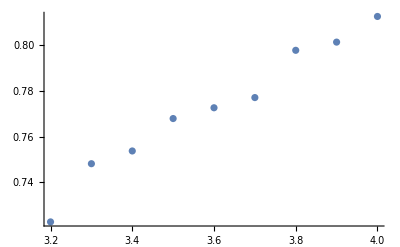

```mathematica
a4={{3.2,74/(3.2×32)},{3.3,79/(3.3×32)},{3.4,82/(3.4×32)},{3.5,86/(3.5×32)}, {3.6,89/(3.6×32)},{3.7,92/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
ListPlot[a4]
```

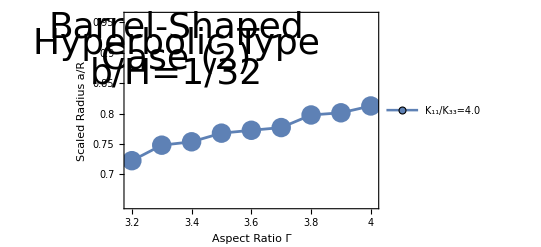

```mathematica
ListPlot[{a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.70,0.75,0.80,0.85,0.9,0.95},None},{{3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.19,4.01},{0.65,0.96}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Right, Bottom}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{3.35,0.94}],Text[Style["Hyperbolic Type",Directive[Black,36]],{3.35,0.915}],Text[Style["Case (2)",Directive[Black,36]],{3.35,0.89}],Text[Style["b/H=1/32",Directive[Black,36]],{3.35,0.865}]}]
```